# AntonAntonov/ReliabilityTools

Reliability-related algorithms and tools

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReliabilityTools.nb"DocumentationEnglishGuidesReliabilityTools.nb

"ReferencePages"

"Symbols"

"AnomalyDetectionInterface.nb"DocumentationEnglishReferencePagesSymbolsAnomalyDetectionInterface.nb

"AnomalyFinder.nb"DocumentationEnglishReferencePagesSymbolsAnomalyFinder.nb

"CrowAMSAAForecast.nb"DocumentationEnglishReferencePagesSymbolsCrowAMSAAForecast.nb

"GNNMonAnomalyDetection.nb"DocumentationEnglishReferencePagesSymbolsGNNMonAnomalyDetection.nb

"GNNMonAnomalyDetector.nb"DocumentationEnglishReferencePagesSymbolsGNNMonAnomalyDetector.nb

"GrowthTrackingPlot.nb"DocumentationEnglishReferencePagesSymbolsGrowthTrackingPlot.nb

"IngestSeeqData.nb"DocumentationEnglishReferencePagesSymbolsIngestSeeqData.nb

"IngestXMLData.nb"DocumentationEnglishReferencePagesSymbolsIngestXMLData.nb

"SimpleAnomalyDetection.nb"DocumentationEnglishReferencePagesSymbolsSimpleAnomalyDetection.nb

"WeibullReliabilityModel.nb"DocumentationEnglishReferencePagesSymbolsWeibullReliabilityModel.nb

"WeibullReliabilityPlot.nb"DocumentationEnglishReferencePagesSymbolsWeibullReliabilityPlot.nb

"Tutorials"

"Outlierdetectionforfinancialtimeseries.nb"DocumentationEnglishTutorialsOutlierdetectionforfinancialtimeseries.nb

"Kernel"

"AnomalyDetectionInterfaces.wl"KernelAnomalyDetectionInterfaces.wl

"AnomalyFinders.wl"KernelAnomalyFinders.wl

"CrowAMSAA.wl"KernelCrowAMSAA.wl

"DataIngestors.wl"KernelDataIngestors.wl

"GrowthTracking.wl"KernelGrowthTracking.wl

"ReliabilityTools.wl"KernelReliabilityTools.wl

"WeibullReliability.wl"KernelWeibullReliability.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Resources"

"sample.xml"Resourcessample.xml

"SeeqFakeSample.xlsx"ResourcesSeeqFakeSample.xlsx

"Tests"

"AnomalyFinder-unit-tests.wlt"TestsAnomalyFinder-unit-tests.wlt

"GNNMonAnomalyDetection-unit-tests.wlt"TestsGNNMonAnomalyDetection-unit-tests.wlt

"IngestSeeqData-unit-tests.wlt"TestsIngestSeeqData-unit-tests.wlt

"IngestXMLData-unit-tests.wlt"TestsIngestXMLData-unit-tests.wlt

"SimpleAnomalyDetection-unit-tests.wlt"TestsSimpleAnomalyDetection-unit-tests.wlt

## Web Content

### Headline Image



### Basic Description

Reliability-related algorithms and know-how encapsulated in convenient model, data, and plotting functions.

### Details

The paclet has several types of functions for doing Reliability Analysis (RA): statistical modeling, visualization graphs, data parsers and converters.

### Primary Context

AntonAntonov`ReliabilityTools`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`ReliabilityTools`"];
```

### Basic Examples

Here is faults data:

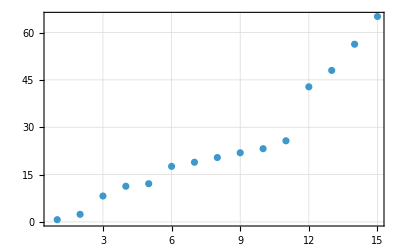

```mathematica
data={0.7,2.4,8.2,11.3,12.1,17.6,18.9,20.4,21.9,23.2,25.7,42.8,48.0,56.3,65.1};
ListPlot[data,PlotRange->All,PlotTheme->"Detailed"]
```

Here the Crow AMSAA method is applied:

```mathematica
CrowAMSAAForecast[data]
```

<|Beta→2.32683,Lambda→0.687065,ChiSquared→12.0623|>

Here is growth tracking plot:

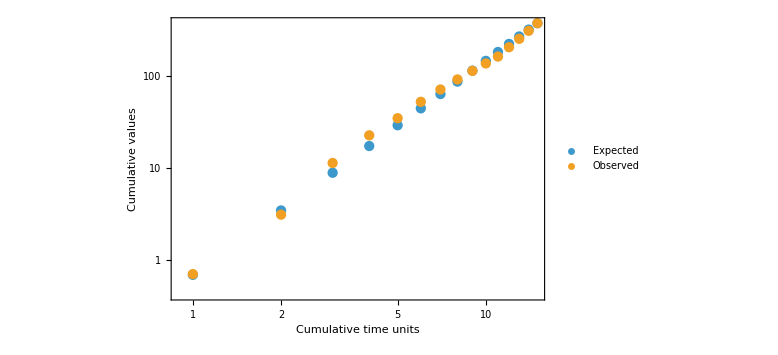

```mathematica
GrowthTrackingPlot[data,ImageSize->Large]
```

Here is Weibull reliability plot:

```mathematica
failureTimes={410,780,1120,1400,1680,1970,2300,2750};
WeibullReliabilityPlot[failureTimes,
"PointColor"->Red,"FittedCurveColor"->Blue,
PlotLabel->Style["Small data","Subsection"],
"Subtitle"->"Demo Weibull plot"
]
```

-Graphics-

### Scope

#### Estimation

#### Data converters

#### Anomaly detection

Here is a time series and its length:

```mathematica
tsData=TimeSeries[…];
```

Here is a date list plot with a vertical grid line that marks the training and testing split date:

```mathematica
splitDate=DateObject[{2024,3,7,12,0,0}];
pl=DateListPlot[tsData,AspectRatio->1/3,ImageSize->Large,PlotLabel->"Temperature, °F",GridLines->{{splitDate},Automatic}]
```

-Graphics-

Here we split the data into training and testing parts:

```mathematica
splitPos=Length@Select[tsData["Times"],#≤AbsoluteTime[splitDate]&];
{training,testing}=TakeDrop[QuantityMagnitude[tsData["Path"]],splitPos];
Length/@{training,testing}
```

{173,115}

Here we get the positions of the anomalies:

```mathematica
pos=AnomalyFinder[{training[[All,2]],testing[[All,2]]},"AnomalyPositions",Method->{"GNNMon","NumberOfNearestNeighbors"->10,"OutlierIdentifier"->"Quartile"}];
Shallow[pos]
```

{1,2,3,4,5,6,7,8,9,10,«98»}

Here is a plot of the time series and the found outliers:

```mathematica
Append[pl,Epilog->{Red,PointSize[0.012],Point[testing[[pos]]]}]
```

-Graphics-

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-ReliabilityTools-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Reliability

Weibull distribution

Probability plot

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/OutlierIdentifiers

AntonAntonov/QuantileRegression

AntonAntonov/MonadicGeometricNearestNeighbors

AntonAntonov/MonadicQuantileRegression

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.